## Nucleation Rate Using in ABF soot.f

```mathematica
(*cbnucl in soot.f using the numbers in soot.h and parameters of A4*)
cbnucl=2.2*√((3.14*4*1.38*10^-16)/(12*1.66*10^-24*16))*(8*10^-8)^2*(6*10^23)^2
```

1.18205×10^37

```mathematica
nucRate=cbnucl*√1800*(10^-10)^2
```

5.015×10^18

```mathematica
A4=10^-10;(*mol/cc*)
mA4=202*10^-3/Subscript[N, A];(*kg*)
σA4=7.1*10^-10;
ωPAH[mA4,mA4,0.0,1800,A4,A4]
ω[mA4,mA4,σA4,σA4,0.0,1800,A4,A4]
Simplify[ω[mA4,mA4,σA4,σA4,0.0,T,Subscript[c, pyrene],Subscript[c, pyrene]]]
```

5.87614×10^-6

5.85392×10^-6

1.37978×10^13 ⅇ^(0./T) √T c_pyrene^2

## Reaction Rate of Reaction 2 & 3 in Violi C&F 2001

```mathematica
Subscript[N, A]=6.02*10^23;(*#/mol*)
Subscript[k, B]=1.38*10^-23(*J/K*);
pre=10^6;(*cc/m^3*)
ω[m1_,m2_,σ1_,σ2_,Ea_,T_,c1_,c2_]:=pre*Subscript[N, A]*((σ1+σ2)/2)^2 √((8*π*Subscript[k, B]*T)/(m1*m2/(m1+m2)))*c1*c2*ⅇ^(-Ea/T) 
(*σ,m,T in SI unit, and Ea in Kelvin, c1 & c2 in mol/cc, then ω in mol/cc/s *)
(*    cc/m^3*#/mol m^2 m/s*[c1]*[c2] = cc/m^3*m^3/(mol s) [c1][c2] = cc/mol/s [c1][c2]  *)
ωPAH[m1_,m2_,Ea_,T_,c1_,c2_]:=pre*Subscript[N, A]*((1.234*(m1*10^3*Subscript[N, A])^0.33*10^-10+1.234*(m2*10^3*Subscript[N, A])^0.33*10^-10)/2)^2 √((8*π*Subscript[k, B]*T)/(m1*m2/(m1+m2)))*c1*c2*ⅇ^(-Ea/T) (*σ,m,T in SI unit, and Ea in Kelvin*)
```

### Reaction 2

```mathematica
Subscript[σ, 1]=5.20*10^-10;(*m,radius of the benzene*)
Subscript[σ, 2]=6.48*10^-10;(*m,radius of the acenaphthylene C12H8*)
Subscript[σ, 12]=(Subscript[σ, 1]+Subscript[σ, 2])/2;
Subscript[m, 1]=78*10^-3/Subscript[N, A](*kg*);
Subscript[m, 2]=152*10^-3/Subscript[N, A](*kg*);
Subscript[E, a]=0.0(*K, 1 kcal= 491 K*);
ω[Subscript[m, 1],Subscript[m, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[E, a],T,Subscript[c, benzene],Subscript[c, IM]]
```

1.3067×10^13 ⅇ^(0./T) √T c_benzene c_IM

#### Plot

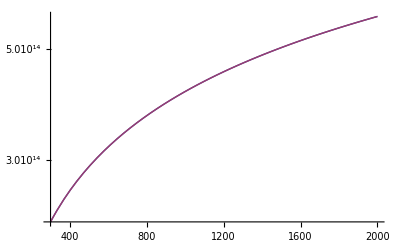

```mathematica
f1[T_]:=1.3*10^13 T^0.5 ⅇ^((6.95*10^-4)/T);(*Why in Violi's paper, a barrier of 1.4*10^-6 kcal/mol is introduced*)
f2[T_]:=1.3*10^13 T^0.5; 
LogPlot[{f1[T],f2[T]},{T,300,2000}]
```

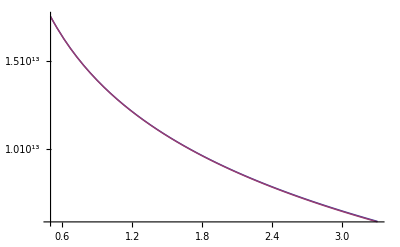

```mathematica
f3[T_]:=1.3*10^13 T^-0.5 ⅇ^(6.95*10^-4 T);(*Why in Violi's paper, a barrier of 1.4*10^-6 kcal/mol is introduced*)
f4[T_]:=1.3*10^13 T^-0.5; 
LogPlot[{f3[T],f4[T]},{T,0.5,3.3}]
```

### Reaction 3

```mathematica
Subscript[σ, 1]=1.2*10^-10;(*m,radius of hydrogen, from wikipedia*)
Subscript[σ, 2]=7.41*10^-10;(*m,diameter of the acenaphthylene C12H8*)
Subscript[σ, 12]=(Subscript[σ, 1]+Subscript[σ, 2])/2;
Subscript[m, 1]=1*10^-3/Subscript[N, A](*kg*);
Subscript[m, 2]=229*10^-3/Subscript[N, A](*kg*);
Subscript[E, a]=0.0(*K, 1 kcal= 491 K*);
ω[Subscript[m, 1],Subscript[m, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[E, a],T,Subscript[c, H],Subscript[c, IM]]
```

5.10913×10^13 ⅇ^(0./T) √T c_H c_IM

## Reaction Rate of Triplet Soot Nucleation

DB5C + A1 ------  IM2 + H;    [I]
IM2 + H ------- P + H2;            [II]
Here, the reaction rate of  reaction [II] by collision theroy:

```mathematica
Subscript[σ, 1]=1.2*10^-10;(*m,radius of hydrogen, from wikipedia*)
Subscript[σ, 2]=8.74*10^-10;(*m,diameter of the acenaphthylene C12H8*)
Subscript[σ, 12]=(Subscript[σ, 1]+Subscript[σ, 2])/2;
Subscript[m, 1]=1*10^-3/Subscript[N, A](*kg*);
Subscript[m, 2]=377*10^-3/Subscript[N, A](*kg*);
Subscript[E, a]=0.0(*K, 1 kcal= 491 K*);
ω[Subscript[m, 1],Subscript[m, 2],Subscript[σ, 1],Subscript[σ, 2],Subscript[E, a],T,Subscript[c, H],Subscript[c, IM]]
```

6.80365×10^13 ⅇ^(0./T) √T c_H c_IM